```mathematica
Clear/@{configurationAdd,configurationMinus,partial,hasEmptyIntersection,simplexes};

SetDirectory[NotebookDirectory[]];

(* These are the types of excitations. You can set their dimensions separately*)
types=1;
n={2,3,2};
dim={0,1,2};
(*The data of simplicial complex is determined by the top-dimensional simplexes. It is a list of simplexes, every simplex is determined by its vertices.*)
topDimensionSimplexes={{1,2,3,4}};
(*If you want to compute localized statistics*)
doLocalization=False;
localizationRegion={1,2,3,4};



simplexes[-1]=={{}};(*There is one (-1)-dimensional simplex*)

(*The set of simplexes in every dimension. simplexes[p] is described by {s1,s2,...sn}, every si is a p-simplex, described by (p+1) vertices.*)
simplexes[dimension_]:=simplexes[dimension]=Union@@(Subsets[#,{dimension+1}]&/@topDimensionSimplexes);

(*A p-chain is described by a Association from simplexes[p] to Integer. The function chainBoundary gives the chain-level boundary with integer coefficient.*)
chainBoundary[chain_,dimension_]:=Module[{boundaryChain=AssociationThread[simplexes[dimension-1],0]},
Do[
Do[
boundaryChain[Delete[s,i]]+=(-1)^(i-1)*chain[s];
,{i,dimension+1}];
,{s,simplexes[dimension]}];
boundaryChain
];

(*We generate the group of all configurations and assign a integer in {1,2,...,dimH} to every configuration as its index*)
cycles=ConstantArray[{},types];
cyclesGenerators=ConstantArray[{},types];
Do[
chains=Association@@@(Thread[simplexes[dim[[type]]+1]->#]&/@Tuples[Range[0,n[[type]]-1],Length[simplexes[dim[[type]]+1]]]);
Do[If[!MemberQ[cycles[[type]],Mod[chainBoundary[chain,dim[[type]]+1],n[[type]]]],AppendTo[cycles[[type]],Mod[chainBoundary[chain,dim[[type]]+1],n[[type]]]];AppendTo[cyclesGenerators[[type]],Values[chain]];]
,{chain,chains}];
,{type,types}]
configurations=Tuples[cycles];
dimH=Length[configurations];
configurationsIndexMap=AssociationThread[configurations->Range[dimH]];

(*These two functions are only used in drawgraph[]*)
configurationGenerators=Flatten/@Tuples[cyclesGenerators];
configurationName[generators_]:=Module[{terms,mathExpr},terms=Table[If[generators[[i]]==1,Subscript["U",i],If[generators[[i]]!=0,Superscript[Subscript["U",i],generators[[i]]],Nothing]],{i,Length[generators]}];
mathExpr=Row[terms,""];
Framed[mathExpr]];

(*Some operations on configurations. The parameter are indexes from 1 to dimH. If you want to customize your excitation model, override "configurations","configurationAdd","configurationMinus","operatorList", "partial","hasEmptyIntersection"*)
configurationAdd[c1_,c2_]:=Module[{b3=ConstantArray[{},types],b1=configurations[[c1]],b2=configurations[[c2]]},
Do[b3[[type]]=Mod[b1[[type]]+b2[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]
configurationMinus[c_]:=configurationMinus[c]=Module[{b3=ConstantArray[{},types],b=configurations[[c]]},
Do[b3[[type]]=Mod[-b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]

(*An operator is described by its type and its corresponding simplex*)
operatorList={};
Do[AppendTo[operatorList,{type,simplex}],{type,types},{simplex,simplexes[dim[[type]]+1]}];
Print[" operatorList:",operatorList];
operatorsIndexMap=AssociationThread[operatorList->Range[Length[operatorList]]];
operatorAmount=Length[operatorList];

dimE=dimH*operatorAmount;
Print["The dimension of Hilbert space is ", dimH];
Print["The dimension of expression group is ", dimE];

(*
The map ∂:F(S)-> A.
An operator s∈S is described by a positive integer k. Then, its inverse s^(-1) is described by -k.
*)
partial[operators_]:=partial[operators]=Module[{multiChain=Table[AssociationThread[simplexes[dim[[t]]+1],0],{t,types}],type,simplex,boundaryMultiChain,x},
Do[{type,simplex}=operatorList[[Abs[id]]];
x=multiChain[[type]];
x[simplex]+=Sign[id];
multiChain[[type]]=x;
,{id,operators}];
boundaryMultiChain=ConstantArray[{},types];
Do[boundaryMultiChain[[type]]=Mod[chainBoundary[multiChain[[type]],dim[[type]]+1],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[boundaryMultiChain]];
];
actOperatorOn[operatorIndex_,configurationIndex_]:=      configurationAdd[configurationIndex,partial[{operatorIndex}] ]   ;


(*Return g^{-1}.*)
processInverse[g_]:=Reverse[-#&/@g];
(*Return g^k.*)
processRepeat[g_,k_]:=Join@@Table[g,k];
(* Return [g1,g2]=g2^{-1}g1^{-1}g2g1. *)
processCommutator[g1_,g2_]:= Join[processInverse[Join[g2,g1]],Join[g1,g2]];
(*Input:{gn,...,g1}. Return:[gn,...,[g2,g1]].*)
processHigherCommutator[operators_]:=Fold[processCommutator[#2,#1]&,Reverse[operators]];

(*The function θ(g,a)*)
theta[operators_,beginning_]:=Module[{configuration,expression},
configuration=beginning;
expression=ConstantArray[0,{Length[operatorList],Length[configurations]}];
Do[If[operator>0,expression[[operator,configuration]]++; configuration=actOperatorOn[operator,configuration];,
configuration=actOperatorOn[operator,configuration];expression[[Abs[operator],configuration]]--;]

,{operator,Reverse[operators]}];
Return[Flatten[expression]];
]


support[operatorID_]:=If[doLocalization,Intersection[operatorList[[operatorID]][[2]],localizationRegion],operatorList[[operatorID]][[2]]];

(*This function directly decides locality identity. If you want to customize some geometry, override this function.*)
hasEmptyIntersection[operators_]:=hasEmptyIntersection[operators]=If[operators=={},False,(Intersection@@(support/@operators)=={})];


isReducedCommutator[fixedOperators_,hArray_]:=Module[{i},
(*If the intersection is not empty, the it is not a identity*)
If[!hasEmptyIntersection[Union[hArray,fixedOperators]],Return[False]];
(* Try throw away some element in hArray. If we cannot do it, then it is reduced*)

For[i=1,i<=Length[hArray],i++,If[hasEmptyIntersection[Union[Delete[hArray,i],fixedOperators]],Return[False]]];
Return[True];
];

(*This function realizes the naive Gauss elimination with pivots ±1*)
pm1Reduce[mat_]:=Module[{dim,rows,pos,rowCounts,colCounts,i,j,val,finished={},nonZeroPosInSameCol,explicitPositions,vec,rules,count,remain,nonZeroPos,pivots},
If[mat=={},Return[{{},{},{}}]];
dim=Length[mat[[1]]];
remain=SparseArray[#,dim]&/@mat;
Monitor[
pivots={};
count=0;
Do[
If[remain[[i]]["ExplicitLength"]>0&&remain[[i]][[Min[remain[[i]]["ExplicitPositions"]]]]<0,remain[[i]]=-remain[[i]];];
,{i,Length[remain]}];
remain=DeleteDuplicates[remain];
While[True,
rows=Length[remain];
rules=Delete[ArrayRules[remain],-1];
nonZeroPos=rules[[All,1]];
If[nonZeroPos=={},Break[]];
pos=Pick[nonZeroPos,Abs[#]==1&/@rules[[All,2]]];
If[pos=={}&&Length[remain]<500,remain=SparseArray[#,dim]&/@LatticeReduce[remain];
rows=Length[remain];
rules=Delete[ArrayRules[remain],-1];
nonZeroPos=rules[[All,1]];
pos=Pick[nonZeroPos,Abs[#]==1&/@rules[[All,2]]];
];
If[pos=={},Break[]];
count++;
rowCounts=BinCounts[nonZeroPos[[All,1]],{1,rows+1}]-1;
colCounts=BinCounts[nonZeroPos[[All,2]],{1,dim+1}]-1;

{i,j}=MinimalBy[pos,rowCounts[[#[[1]]]]*colCounts[[#[[2]]]]&][[1]];
val=remain[[i]][[j]];
vec=remain[[i]];
AppendTo[pivots,j];
AppendTo[finished,vec];
nonZeroPosInSameCol=#[[1]]&/@Cases[nonZeroPos,{_,j}];

remain[[nonZeroPosInSameCol]]=SparseArray[remain[[#]]-(val*remain[[#]][[j]])*vec,dim]&/@nonZeroPosInSameCol;
If[remain[[#]]["ExplicitLength"]>0&&remain[[#]][[Min[remain[[#]]["ExplicitPositions"]]]]<0,remain[[#]]=-remain[[#]];]&/@nonZeroPosInSameCol;
remain=DeleteDuplicates[remain];

];
(*output=Union[output,SparseArray[#,dim]&/@HermiteDecomposition[m][[2]]];*)
If[Length[remain]<500,remain=SparseArray[#,dim]&/@LatticeReduce[remain];];
(*Print["Remaining rows: ",Length[remain]];
Print["Total Rank: ",If[remain=={},Length[finished],Length[finished]+MatrixRank[remain]]];*)
,{count,Length[remain],Length[nonZeroPos]}];
Return[{finished,remain,pivots}]
]
(*This function is not used yet.

pm1ReduceWithGivenPivots[part1_,part2_,pivots_]:=Module[{dim=Length[part1[[1]]],pos,i,j,val,nonZeroPosInSameCol,vec,rules,count,remain,nonZeroPos,finished,remain1,pivots1},
remain=SparseArray[#,dim]&/@part2;
Monitor[

count=0;
Do[
If[remain[[i]]["ExplicitLength"]>0&&remain[[i]][[Min[remain[[i]]["ExplicitPositions"]]]]<0,remain[[i]]=-remain[[i]];];
,{i,Length[remain]}];
remain=DeleteDuplicates[remain];

Do[
count++;
vec=part1[[i]];
j=pivots[[i]];

val=vec[[j]];

rules=Delete[ArrayRules[remain],-1];
nonZeroPos=rules[[All,1]];
nonZeroPosInSameCol=#[[1]]&/@Cases[nonZeroPos,{_,j}];

remain[[nonZeroPosInSameCol]]=SparseArray[remain[[#]]-(val*remain[[#]][[j]])*vec,dim]&/@nonZeroPosInSameCol;
If[remain[[#]]["ExplicitLength"]>0&&remain[[#]][[Min[remain[[#]]["ExplicitPositions"]]]]<0,remain[[#]]=-remain[[#]];]&/@nonZeroPosInSameCol;
remain=DeleteDuplicates[remain];

,{i,Length[pivots]}];

,{count,Length[remain],Length[nonZeroPos]}];
{finished,remain1,pivots1}=pm1Reduce[remain];

Return[{Join[part1,finished],LatticeReduce[remain1],Join[pivots,pivots1]}];
]
*)
(*
After initialize nessasary functions, run this. Result is stored in variables.
"finished" contains expressions that used to elimate other entries at "pivots".
"remains" contains remaining expressions without any ±1, so the naive Gauss elimation stops here. Length[remains] is usually small, and one can simply read out the statistics from it.
"identities"="finished"+"remains" generates Eid.
*) 
computeStatistics[]:=Module[{comms={},localIdentities={},a,b,c,i,j},
identities={};
Monitor[
Do[
comms={};
localIdentities={};
Do[
If[isReducedCommutator[{i,j},hArray],AppendTo[comms,processHigherCommutator[{#}&/@Join[hArray,{i,j}]]];];

,{hArray,Subsets[Range[i+1,operatorAmount],5]}];
Do[localIdentities=Join[localIdentities,theta[comm,#]&/@Range[dimH]],{comm,comms}];
localIdentities=Join[#[[1]],#[[2]]]&[pm1Reduce[localIdentities]];
identities=Join[identities,localIdentities];


,{i,1,operatorAmount-1},{j,i+1,operatorAmount}];,StringForm["Computing [``,``]",i,j]];

Print["Doing joining process..."];
Print["time:",AbsoluteTiming[
{finished,remains,pivots}=pm1Reduce[identities];][[1]]];
identities=Join[finished,remains];
(*Print[remains];*)
]

(* This version seems to run slower

computeStatistics[]:=Module[{part2,f=ConstantArray[{},{operatorAmount,operatorAmount}],pivots,remain,finished,i,j},
finished={};
Print["Time:",AbsoluteTiming[
Module[{comms={},localIdentities={},a,b,c},
Monitor[
Do[
comms={};
localIdentities={};
Do[

If[isReducedCommutator[{i,j},hArray],AppendTo[comms,processHigherCommutator[{#}&/@Join[hArray,{i,j}]]];];

,{hArray,Subsets[Range[i+1,operatorAmount],5]}];
Do[localIdentities=Join[localIdentities,theta[comm,#]&/@Range[dimH]],{comm,comms}];
{a,b,c}=pm1Reduce[localIdentities];
If[i==1&&j==2,pivots=c;remain=b;finished=a;];

f[[i,j]]=Join[a,b];

,{i,1,operatorAmount-1},{j,i+1,operatorAmount}],StringForm["Computing [``,``]",i,j]];
];

Print["Doing joining process..."];
Monitor[


Do[part2=remain;
Do[part2=Join[part2,f[[i,j]]],{i,1,j-1}];
{finished,remain,pivots}=pm1ReduceWithGivenPivots[finished,part2,pivots];
,{j,3,operatorAmount}];
,StringForm["Step: ``/``",j,operatorAmount]];
Print["Total Rank: ",If[remain=={},Length[finished],Length[finished]+MatrixRank[remain]]];

Print[remain];
identities=Join[finished,remain];
][[1]]];
];
*)
```

operatorList:{{1,{1,2}},{1,{1,3}},{1,{1,4}},{1,{2,3}},{1,{2,4}},{1,{3,4}}}

The dimension of Hilbert space is 8

The dimension of expression group is 48

```mathematica
computeStatistics[]
```

Doing joining process...

time:0.0353043

```mathematica
remains
```

{SparseArray[…]}

```mathematica
(*delta[θ(g,a),b]=θ(g,a+b)*)
delta[expression_,configuration_]:=Module[{rules,newRules},
rules=Delete[ArrayRules[expression],-1];
newRules=((#[[1,1]]-Mod[#[[1,1]]-1,dimH]-1+configurationAdd[configuration,1+Mod[#[[1,1]]-1,dimH]])->#[[2]])&/@rules;
Return[SparseArray[newRules,dimE]]
]
(*Help you visualize your expression*)
drawGraph[expression_]:=Module[{nodes,edges,expressionMatrix},
nodes={};
edges={};
expressionMatrix=Partition[expression,dimH];
Do[
If[expressionMatrix[[op,configuration]]!=0,AppendTo[edges,Labeled[Style[DirectedEdge[configuration,actOperatorOn[Abs[op],configuration]],If[expressionMatrix[[op,configuration]]>0,Red,Blue]],Style[Subscript[(ToString[expressionMatrix[[op,configuration]]]<>"×U"), op],FontSize->20]]
];nodes=Union[nodes,{configuration,actOperatorOn[op,configuration]}];];
 
,{op,Range[Length[operatorList]]},{configuration,Range[dimH]}];
Graph[edges,VertexLabels->Table[v->configurationName[configurationGenerators[[v]]],{v,nodes}]]
]

(*A tool to simplify an expression. It does not always work.*)
simplifyExpressionRandomly[expression_,yourExpect_]:=Block[{exp,temp,c,pool,largePool},
exp=expression;
While[True,
Do[
largePool=Select[identities,Abs[8*#.exp]>#.#&];
Do[
pool=Select[largePool,Abs[2*#.exp]>#.#&];
If[pool=={},Break[];];
temp=RandomChoice[pool];
exp=exp-Sign[temp.exp]*temp;
,1000000];
If[Select[identities,Abs[2*#.exp]>#.#&]=={},Break[]];
,1000000];
If[exp.exp<=yourExpect,Break[];];
];
Return[SparseArray[exp,dimE]];
]
(*This function may help you check whether a expression is statistical or a locality identity*)
expressionReduce[identities_,expressionInput_,pivots_]:=Module[{dim=Length[expressionInput],pos,i,j,val,nonZeroPosInSameCol,vec,rules,count=0,exp=expressionInput},
Monitor[

Do[
count++;
vec=identities[[i]];
j=pivots[[i]];

val=vec[[j]];

exp=SparseArray[exp-(val*exp[[j]])*vec,dim];
,{i,Length[pivots]}];

,{count,exp.exp}];
Return[exp];
]
```

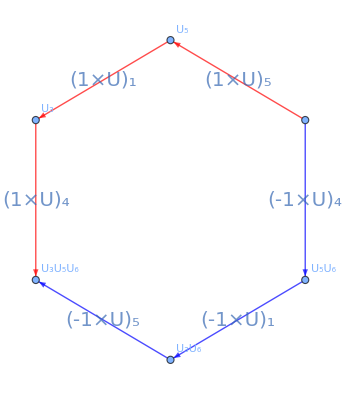

```mathematica
drawGraph[remains[[1]]/4]
```

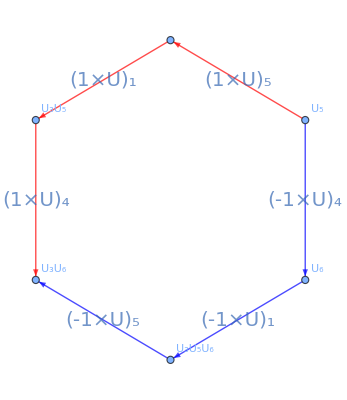

```mathematica
drawGraph[delta[remains[[1]]/4,actOperatorOn[5,1]]]
```

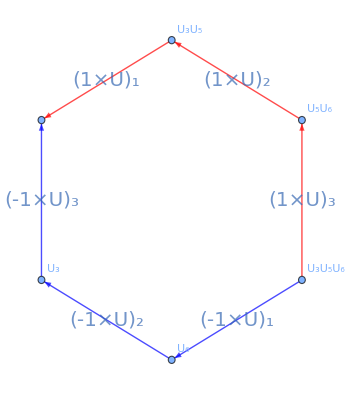

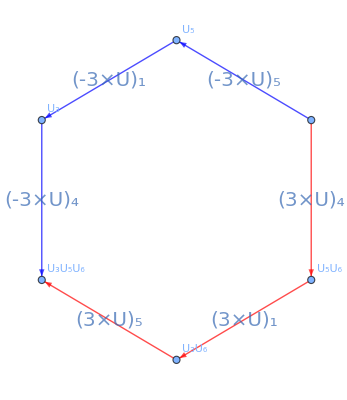

```mathematica
drawGraph[theta[{1,2,3,-1,-2,-3},1]]
drawGraph[expressionReduce[identities,theta[{1,2,3,-1,-2,-3},1],pivots]]
```